```mathematica
y=2009;
```

```mathematica
dowJonesMember={"MMM","AXP","AAPL","BA","CAT","CVX","CSCO","KO","DD","XOM","GE","GS","HD","INTC","IBM","JNJ","JPM","MCD","MRK","MSFT","NKE","PFE","PG","TRV","UNH","UTX","VZ","WMT","DIS"};
```

```mathematica
stocksSets=splitup[dowJonesMember,5];
Length/@stocksSets
```

{5,6,6,6,6}

```mathematica
trainingSets=Flatten[Drop[stocksSets,{#}]]&/@Range[Length[stocksSets]];
testSets=stocksSets[[#]]&/@Range[Length[stocksSets]];
```

```mathematica
trainingSet=x[2005,2012]/@dowJonesMember;
```

```mathematica
trainingSets=splitup[trainingSet,5];
```

```mathematica
trainingSets=Function[n,
Flatten[Drop[trainingSets,{n}],2]]/@Range[Length[trainingSets]];
```

```mathematica
Dimensions/@trainingSets
```

{{42288,64},{40526,64},{40526,64},{40526,64},{40526,64}}

```mathematica
{Φs,As,bs}=Transpose[Φ/@trainingSets];
```

```mathematica
trainingReturns=r[2005,2012]/@dowJonesMember;
```

```mathematica
trainingReturns=splitup[testReturns,5];
```

```mathematica
trainingReturns=Function[n,
Flatten[Drop[trainingReturns,{n}]]]/@Range[Length[trainingReturns]];
```

```mathematica
Dimensions/@trainingReturns
```

{{42288},{40526},{40526},{40526},{40526}}

```mathematica
qs=MapThread[findQ[0,1,#1,#2]&,{Φs,trainingReturns}];
```

```mathematica
Norm/@qs
```

{1.,1.,1.,1.,1.}

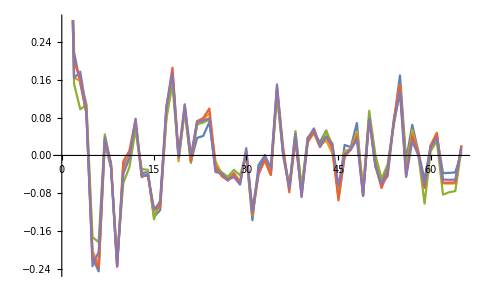

```mathematica
ListLinePlot[qs]
```

```mathematica
testFeatures=x[2012,2015]/@dowJonesMember;
testReturns=r[2012,2015]/@dowJonesMember;
```

```mathematica
getCumulativeReturns[fold_]:=
Module[{},
normalizedTestFeatures=Φ[#,As[[fold]],bs[[fold]]]&/@testFeatures;
allocations=Transpose[
Function[Xs,
Xs.qs[[fold]]]/@normalizedTestFeatures
];
pickedAllocations=Max/@result;
pickedStocks=Flatten[MapThread[Position,{result,pickedAllocations}]];
pickedReturns=MapThread[Part,{Transpose[testReturns],stocksToPick}];
totalReturns=pickedReturns*pickedAllocations+Rf(1-pickedAllocations);

cumulativeReturns=FoldList[Times,1,1+totalReturns]
];
```

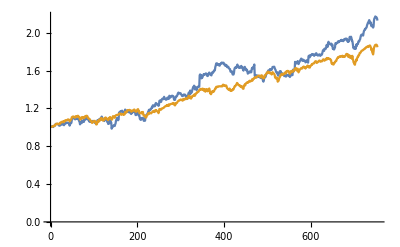

```mathematica
ListLinePlot[{getCumulativeReturns[3]}~Join~{rawCumulativeReturns}]
```

```mathematica
Last/@(getCumulativeReturns/@Range[5])
```

{2.12802,2.12802,2.12802,2.12802,2.12802}

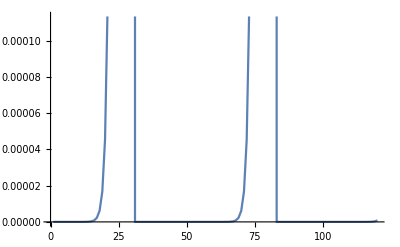

```mathematica
ListLinePlot[weekFeature[30][Range[120]]]
```

```mathematica
weekFeature[30][30]
```

1.

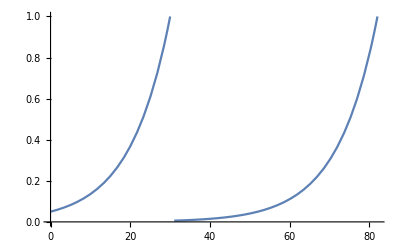

```mathematica
Plot[weekFeature[30][x],{x,0,82},PlotRange->{0,1}]
```

```mathematica
weekFeature[30][31]//N
```

0.600496

```mathematica
dowJonesReturns=r[2000]/@dowJonesMember;
```

{{-0.0397351,0.0289655,0.080429,0.0198513,-0.00486615,-0.0171151,3840,-0.00310005,0.00408537,-0.0304245,-0.00419635,-0.00635266,0.00221547},27,{1}}
 |  |  |  |

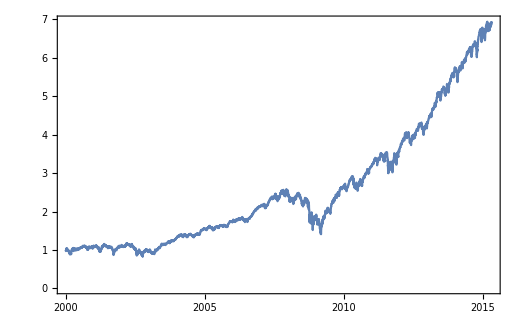

```mathematica
DateListPlot[Transpose[{dowJonesDates,FoldList[Times,1,1+Mean[dowJonesReturns]]}]]
```

```mathematica
{dowJonesDates,prices}=Transpose[FinancialData["AAPL","Price",{2000}]];
```